0.0387345+0.184129 x

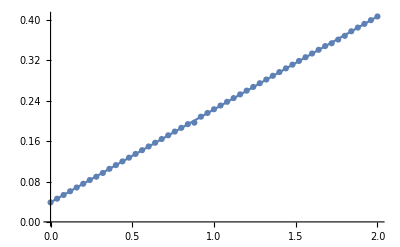

```mathematica
ga={{0.00,0.03857290},{0.04,0.04597210},{0.08,0.05337046},{0.12,0.06076827},{0.16,0.06816549},{0.20,0.07556097},{0.24,0.08295569},{0.28,0.08954219},{0.32,0.09692104},{0.36,0.10513149},{0.40,0.11252145},{0.44,0.11991034},{0.48,0.12729850},{0.52,0.13468433},{0.56,0.14207001},{0.60,0.14945364},{0.64,0.15683657},{0.68,0.16421745},{0.72,0.17159611},{0.76,0.17897703},{0.80,0.18635479},{0.84,0.19373182},{0.88,0.19661019},{0.92,0.20848085},{0.96,0.21585489},{1.00,0.22322556},{1.04,0.23059595},{1.08,0.23796396},{1.12,0.24533087},{1.16,0.25269712},{1.20,0.26006402},{1.24,0.26742699},{1.28,0.27478983},{1.32,0.28215072},{1.36,0.28950920},{1.40,0.29686916},{1.44,0.30422431},{1.48,0.31157963},{1.52,0.31893349},{1.56,0.32628614},{1.60,0.33363747},{1.64,0.34098661},{1.68,0.34833479},{1.72,0.35395754},{1.76,0.36130032},{1.80,0.36864871},{1.84,0.37771228},{1.88,0.38505231},{1.92,0.39238711},{1.96,0.39973092},{2.00,0.40706640}};
f=Fit[ga,{1,x},x]
Show[
ListPlot[ga],
Plot[f,{x,0,2}]
]
```

```mathematica
f/.x->2
```

0.406992